Bernstein-Vazirani Algorithm |

Quantum Implementationpaclet:Q3/tutorial/BernsteinVaziraniAlgorithm#89537285 | Examplepaclet:Q3/tutorial/BernsteinVaziraniAlgorithm#453826057

See also Section 4.2 of the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

Suppose that we are given a binary function f:{0,1}^n→{0,1}, the value of which is determined by a secret string s of n bits

f:x↦x·s   (mod 2).

The Bernstein-Vazirani problem finds the secret bit string s by making queries to the oracle f. Classically, one needs n queries to the function f to infer the secret string s.

Oraclepaclet:Q3/ref/OracleQ3 Package Symbol | Represents a quantum implementation of classical oracle.
Hadamardpaclet:Q3/ref/HadamardQ3 Package Symbol | The Hadamard gate on a single qubit.

Q3 functions used in the Bernstein-Vazirani algorithm.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Quantum Implementation

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

The Bernstein-Vazirani algorithm (Bernstein & Vazirani, 1993, 1997) is implemented in the same quantum circuit as the Deutsch-Jozsa algorithm, only that the analysis of the final readout is different.

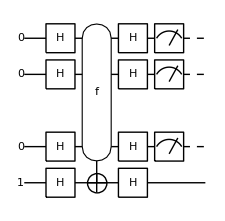

```mathematica
qc=QuantumCircuit[Ket[S[4]->1,S@{1,2,3,4}],
S[{1,2,3,4},6],
Oracle[f,S@{1,2,3},S[4]],
S[{1,2,3,4},6],
Measurement[S[{1,2,3},3]],
"Invisible"->S[2.5]]
```

The first set of the Hadamardpaclet:Q3/ref/HadamardQ3 Package Symbol gates and the quantum oracle leads the n-qubit register to the state

1/2^(n/2)∑_(x=0)^(2^n-1) (x(-1))^(x·s).

Taking the inverse of the mapping

H^(⊗n)y^(⊗n)=1/2^(n/2)∑_(x=0)^(2^n-1) (x(-1))^(x·y),

where x·y denotes the bitwise inner product

x·y:=x_1 y_1+x_2 y_2+⋯+x_n y_n  (mod 2),

one can observe that the second set of the Hadamardpaclet:Q3/ref/HadamardQ3 Package Symbol gates converts the above state to the final state s that is set by the secret bit string. Therefore, a simple measurement of the final state in the logical basis will just reveal the secret string.

Example

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this example, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Consider a secrete string of bits. The task is to find the secrete string.

```mathematica
string={0,1};
```

In the Bernstein-Vazirani algorithm, the value of the classical oracle f is determined by the given secrete string.

```mathematica
Clear[f];
f[x__]:=Mod[{x}.string,2]
```

For example, f[1,1]=0·1 + 1·1=1.

```mathematica
f[1,1]
```

1

Here is a quantum circuit of the Bernstein-Vazirani algorithm. The final Hadamard gate on the third qubit is not necessary, and we put it here to make the output state more readable.

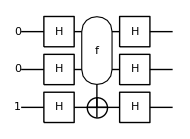

```mathematica
cc={1,2};
tt={3};
all={1,2,3};
qc=QuantumCircuit[Ket[S[3]->1,S@all],S[all,6],Oracle[f,S@cc,S@tt],S[all,6]]
```

```mathematica
out=ExpressionFor[qc]
```

0_S_11_S_21_S_3

Here is the secrete string successfully retrieved.

```mathematica
answer=out[S@cc]
```

{0,1}

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Decision Algorithms
▪Quantum Algorithms
▪Quantum Information Systems with Q3

| Related Links
▪E. Bernstein and U. Vazirani (1993)https://doi.org/10.1145/167088.167097,  in Proceedings of the 25th Annual ACM Symposium on the Theory of Computing (ACM Press, 1993), pp. 11–20, "Quantum Complexity Theory."
▪E. Bernstein, and U. Vazirani, SIAM Journal on Computing 26, 1411 (1997)https://doi.org/10.1137/s0097539796300921, "Quantum Complexity Theory."
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press, 2011).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).